```mathematica
Needs["dsvsolve`"];
```

## Input

Edit or simply evaluate the following cell to see the input

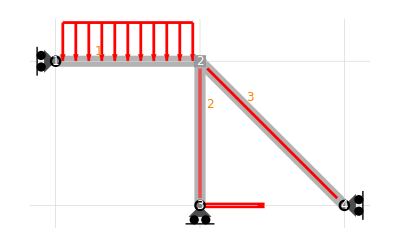

```mathematica
example={$$nodes->{{-L, L}, {0, L}, {0, 0}, {L, 0}},
$$edges->{{1, 2}, {2, 3}, {2, 4}},$$absname->s,
$$constraints->{{{"rollv", 1}}, {{"clamp", 1, 2}, {"clamp", 2, 3}}, {{"rollh", 2}}, {{"rollv", 3}}},
$$bodyloads->{{1, {0, -q, 0}}},
$$nodalloads->{{3, {q*L, 0, 0}}},
$$predeformations->{{1, {0, 0, 0}}},
$$cdisplacements->{{1, {0, 0, 0}}},
$$EIoverEAL2->0};
(*All constraints are initialized to hinge constraints; use "BFConstraintsPalette[BFConstraintTypes];" to input different constraints.*)
BFShowInput[example]
```

## Output

Evaluate the following cell to solve the problem and see the output

```mathematica
BFClassify[example]; sol = {{Ns, Qs, Ms}, details} = BFForcesSolve[example];
(*A=Transpose[First[BFStaticProblem[example]]];MatrixForm[A]
BFShowRigidMotions[example]*)
(*BFEquations[example,"Nodal"]; sol = {{us, vs}, {Ns, Qs, Ms}, details} = BFDisplacementsSolve[example];*)
gsol=BFShowOutput[example, sol]
```

BFClassify::sd: Statically determined system.

BFClassify::kd: Kinematically determined system.

123

Evaluate the following cell to print the above output

```mathematica
CellPrint/@Rest/@Last[sol];
Print/@Cases[gsol,Graphics[___],Infinity];
```

Dimensionless abscissa

s

Static equilibrium matrix

{{-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,0,L,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,0,L,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,√2 L,1},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-2,0,0,0,2,0,0,0,0,√2,√2,0,0,0,0},{0,0,0,0,-2,0,-2,0,0,0,0,0,-√2,√2,0,0,0,0},{0,0,0,0,0,-1,0,0,1,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1}}

Static equilibrium vector

{0,L q,(L^2 q)/2,0,0,0,0,0,0,0,0,0,0,0,-L q,0,0,0}

Fredholm condition: are the loads orthogonal to allowed rigid motions?

True

Degree of static undetermination

0

Reactions

{{-(L q)/2,0,0,-(L q)/2,L q,-(L^2 q)/2},{-L q,L q,L^2 q,-L q,L q,0},{-(3 L q)/(2 √2),-(3 L q)/(2 √2),-(3 L^2 q)/2,-(3 L q)/(2 √2),-(3 L q)/(2 √2),0}}

Internal actions (N,Q,M)

{{-(L q)/2,-L q,-(3 L q)/(2 √2)},{L q s,L q,-(3 L q)/(2 √2)},{-1/2 L^2 q s^2,1/6 (6 L^2 q-6 L^2 q s),1/6 (-9 L^2 q+9 L^2 q s)}}

-Graphics-

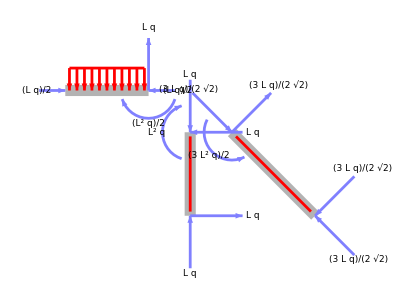

-Graphics-

-Graphics-

-Graphics-